```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fRandomSampler[aX_,aStepSize_]:=RandomVariate[NormalDistribution[aX,aStepSize],{1}][[1]]
fStep[aX_,aStepSize_]:=Module[{aNew=fRandomSampler[aX,aStepSize]},If[Or[aNew<0,aNew>10],fStep[aX,aStepSize],aNew]]
fSteps[aNumberSteps_,aStart_,aStepSize_]:=NestList[fStep[#,aStepSize]&,aStart,aNumberSteps]
options3={Frame->{True,True,False,False},FrameStyle->{{Thickness[0.005],Black},{Thickness[0.005],Black}},BaseStyle->{FontSize->30},LabelStyle->Black};
```

```mathematica
lTest=fSteps[1000000,5,1];
```

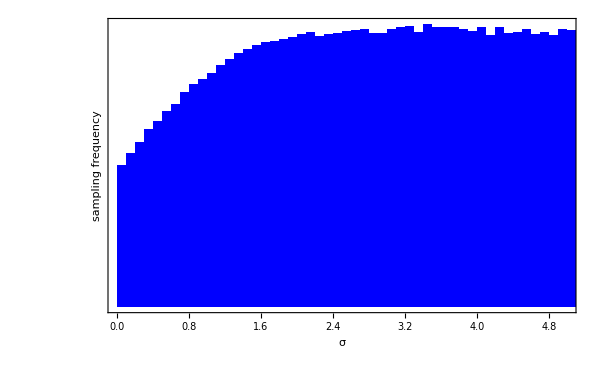

```mathematica
g1=Histogram[lTest,100,PlotRange->{{0,5},Full},Evaluate@options3,ChartStyle->Blue,FrameTicks->{True,None},FrameLabel->{"σ","sampling frequency"},ImageSize->600]
```

```mathematica
Export["metropolisHastings_underSampling.pdf",g1]
```

metropolisHastings_underSampling.pdf